```mathematica
$MinPrecision=$MaxPrecision=9;
p=0.95
```

0.95

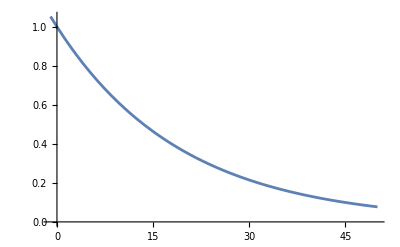

```mathematica
Plot[p^x, {x, -1, 50}]
```

```mathematica
f[x_,y_]:=Piecewise[{{p^y,x==0},{p^x,y==0},{(p^x)^y,True}}]
Plot3D[f[x,y],{x,0,40},{y,0,40},AxesLabel->{"x","y","f(x, y)"},PlotRange->All]
```

-Graphics3D-

```mathematica
DFSPlot3D[n_,{startI_,startJ_},p_,figSize_:10]:=Module[{matrix,v,helper,plot2D,plot3D},(*Initialize the matrix and set*)matrix=ConstantArray[0,{n,n}];
v={};
(*Define the helper function*)helper[i_,j_,pAcc_,up_]:=Module[{nei},If[i<1||i>n||j<1||j>n||MemberQ[v,{i,j}],Return[]];
AppendTo[v,{i,j}];
matrix[[i,j]]=pAcc;
(*Calculate neighbors based on direction*)nei=If[up==1,{{i+1,j},{i+1,j+1},{i+1,j-1},{i,j-1},{i,j+1}},{{i-1,j},{i-1,j+1},{i-1,j-1},{i,j-1},{i,j+1}}];
(*Recursion*)Do[helper[nei[[k,1]],nei[[k,2]],pAcc*p,up],{k,Length[nei]}]];
(*Perform DFS in both directions*)helper[startI,startJ,1,1];
v={};(*Clear the set*)helper[startI,startJ,1,0];
plot2D=MatrixPlot[matrix,ColorFunction->"AvocadoColors",ImageSize->figSize*50,PlotLegends->Automatic,PlotLabel->"DFS Traversal Levels",FrameTicks->None];
plot3D=ListPlot3D[matrix,ColorFunction->"AvocadoColors",ImageSize->figSize*50,PlotLabel->"DFS Traversal Levels 3D",DataRange->{{0,n-1},{0,n-1}},PlotRange->{All,All,{0,1}}];
{plot2D,plot3D}];
DFSPlot3D[100,{50,50},0.94,8]
```

{-Graphics-,-Graphics3D-}

```mathematica
f[x_,y_]:=(p^Abs[x])*(p^Abs[y])
Plot3D[f[x,y],{x,-50,50},{y,-50,50}, PlotRange->{0,1}, ColorFunction->"AvocadoColors"]
```

-Graphics3D-

```mathematica
g[x_,y_]:=(p^x)*(p^y)
Plot3D[g[x,y],{x,0,50},{y,0,50}, PlotRange->{0,1}, ColorFunction->"AvocadoColors"]
```

-Graphics3D-

```mathematica
partialDerivativeX=D[f[x,y],x]
partialDerivativeY=D[f[x,y],y]
indefiniteIntegralX=Integrate[f[x,y],x]
indefiniteIntegralY=Integrate[f[x,y],y]
```

-0.0512933 0.95^(Abs[x]+Abs[y]) Abs'[x]

-0.0512933 0.95^(Abs[x]+Abs[y]) Abs'[y]

∫0.95^(Abs[x]+Abs[y])ⅆx

∫0.95^(Abs[x]+Abs[y])ⅆy

```mathematica
Integrate[Integrate[f[x,y],{x, -Infinity, Infinity}], {y, -Infinity, Infinity}]
```

1520.33

```mathematica
f[x_,y_, p_]:=(p^Abs[x])*(p^Abs[y])
Integrate[Integrate[Integrate[f[x,y, q],{q, 0, 0.8}],{x, -Infinity, Infinity}], {y, -Infinity, Infinity}]
```

9.8045

```mathematica
NIntegrate[f[x,y,p],{x,-Infinity,Infinity},{y,-Infinity,Infinity}, {p,0,0.8}, Method->{"GlobalAdaptive","MaxErrorIncreases"->10000,"MaxRecursion"->50}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

9.8045

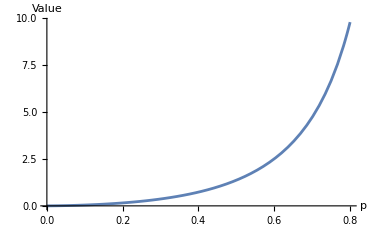

```mathematica
integralFunction[q_?NumericQ]:=NIntegrate[f[x,y,p],{x,-Infinity,Infinity},{y,-Infinity,Infinity}, {p,0,q}, Method->{"GlobalAdaptive","MaxErrorIncreases"->10000,"MaxRecursion"->50}]
Plot[{integralFunction[x]},{x,0,0.8},PlotRange->All,AxesLabel->{"p","Value"}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

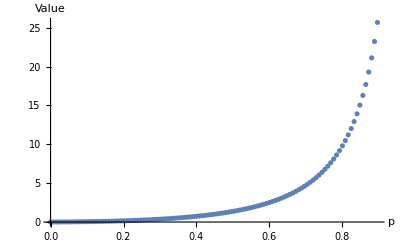

FittedModel[-1.79859+1.79859/(1-1.04664 q)]

{a→1.79859,b→1.04664}

| Estimate | Standard Error | Confidence Interval
a | 1.79859 | 0.033824 | {1.73156,1.86561}
b | 1.04664 | 0.00177402 | {1.04312,1.05015}

```mathematica
qValues=Range[0,0.9,0.008]; (*Adjust the range and step size as needed*)
values=Table[{q,integralFunction[q]},{q,qValues}];
ListPlot[values,PlotRange->All,AxesLabel->{"p","Value"}]
model[q_,a_,b_]:=a/(1-b*q)-a
fit=NonlinearModelFit[values,model[q,a,b],{a,b},q]
fit["BestFitParameters"]
fit["ParameterConfidenceIntervalTable"]
```

```mathematica
model[q_,a_,b_,c_]:=a/((1-b*q)^c)-a
fit=NonlinearModelFit[values,model[q,a,b,c],{a,b,c},q]
fit["BestFitParameters"]
fit["ParameterConfidenceIntervalTable"]
```

FittedModel[-0.370128+0.370128/(1-0.886137 q)^2.68563]

{a→0.370128,b→0.886137,c→2.68563}

| Estimate | Standard Error | Confidence Interval
a | 0.370128 | 0.0135083 | {0.343358,0.396899}
b | 0.886137 | 0.00529384 | {0.875646,0.896628}
c | 2.68563 | 0.0604843 | {2.56577,2.8055}

```mathematica
Integrate[p^(Abs[x]+Abs[y]),{x,0,Infinity},{y,0,Infinity}]
```

Piecewise[{{1/Log[p]^2, Re[Log[p]]<0}, {Integrate[p^(Abs[x]+Abs[y]),{x,0,∞},{y,0,∞},Assumptions→Re[Log[p]]≥0], True}}]

```mathematica
Integrate[4/Log[p]^2, p]
```

4 (-p/Log[p]+LogIntegral[p])

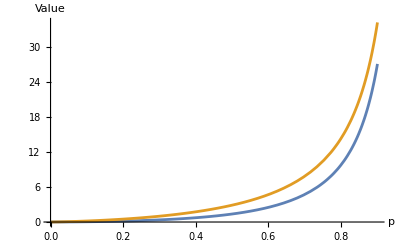

```mathematica
Plot[{4 (-p/Log[p]+LogIntegral[p]), 4 (-p/Log[p])},{p,0,0.9},PlotRange->All,AxesLabel->{"p","Value"}]
```

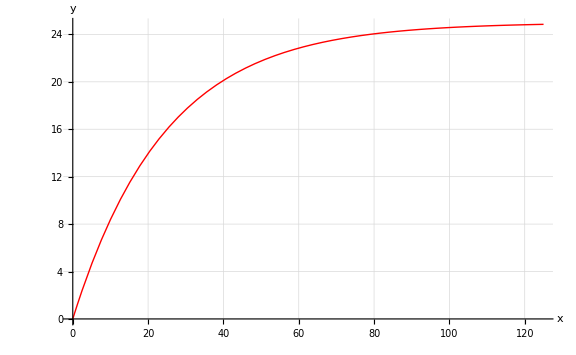

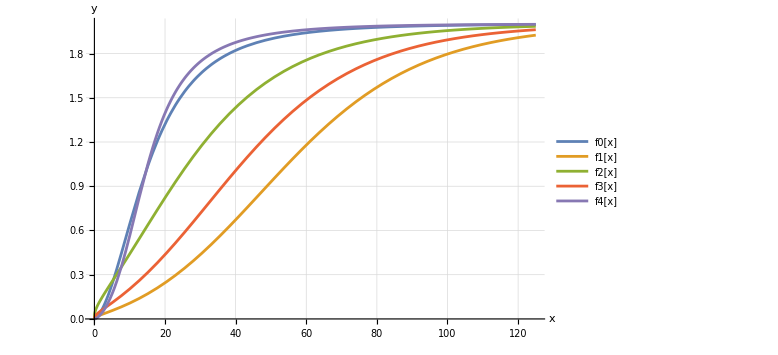

```mathematica
n=5;
b[x_]:=n^2 (1-(1-(1/n^2))^x);
g[x_]:=4(-x/Log[x]+LogIntegral[x])
f0[x_]:=2*(g[b[x]/n^2])/(g[b[x]/n^2] +1)
f1[x_]:=2*(g[b[x]/n^2])/(g[b[x]/n^2] +b[x])
f2[x_]:=2*(g[b[x]/n^2])/(g[b[x]/n^2] +b[x]/n)
f3[x_]:=2*(g[b[x]/n^2])/(g[b[x]/n^2] +b[x]/2)
f4[x_]:=4/Pi *ArcTan[g[b[x]/n^2]]
Plot[{b[x]},{x,0,5*n^2},PlotRange->All, PlotStyle->{{Thick,Red},{Thick,Blue,Dashed}},AxesLabel->{"x","y"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}]
Plot[{f0[x], f1[x], f2[x], f3[x], f4[x]},{x,0, 5*n^2 },PlotRange->All,AxesLabel->{"x","y"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}, PlotLegends->Placed[LineLegend[Automatic,{"f0[x]","f1[x]","f2[x]","f3[x]","f4[x]"}],Right]]
```

# Análisis Complejidad (Por fin😬☠)

RayoCosmico:

```mathematica
TexForm[(1-b[x]/n^2)*n^(2*(g[b[x]/n^2])/(g[b[x]/n^2]+b[x]/2))]
```

TexForm[5^(-2 x-(8 (1-(24/25)^x))/((25/2 (1-(24/25)^x)-(4 (1-(24/25)^x))/Log[1-(24/25)^x]) Log[1-(24/25)^x])) 24^x]

```mathematica
Simplify[(1-b[x]/n^2)*n^(2*(g[b[x]/n^2])/(g[b[x]/n^2]+b[x]/2)), Assumptions->{n>0,x>0,b[x]>0,Element[n|x|b[x],Reals]}]
```

5^((2 5^(-2 x) (-24^x+25^x) (8-8 x+25 x Log[1-(24/25)^x]))/((-1+(24/25)^x) (-8+25 Log[1-(24/25)^x]))) 24^x

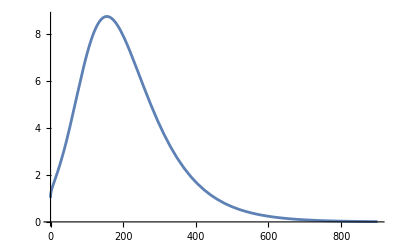

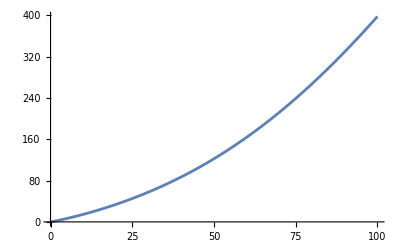

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {155.853}. NIntegrate obtained 933.123 and 18.6378 for the integral and error estimates.

933.123

```mathematica
n=10;
rc[x_]:=(1-b[x]/n^2)*n^(2*(g[b[x]/n^2])/(g[b[x]/n^2] +b[x]/Power[n, 1.57]))
Plot[{rc[x]},{x, 0, 900}]
Plot[{NIntegrate[rc[x], {x, 0, q}]},{q, 0, 100}]
NIntegrate[rc[x], {x, 0, Infinity}]
```

10

155.081

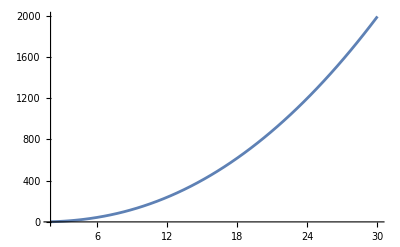

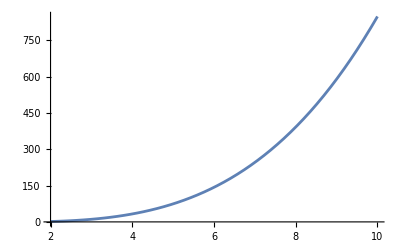

```mathematica
n=10
puntoEstab:=Module[{result},result=NMaximize[{rc[x], x>0},x];
xOptimal=x/. result[[2]];xOptimal]
puntoEstab
Plot[{puntoEstab},{n, 2, 30}]
Plot[{NIntegrate[rc[x], {x, 0, puntoEstab}]},{n, 2, 10}]
```

```mathematica
points=Flatten[Cases[Plot[{NIntegrate[rc[x],{x,0,puntoEstab}]}, {n,2,700}],Line[data_]:>data,Infinity], 1]
```

{{2.00001,1.63945},{2.21409,2.79866},{2.42816,4.34311},{2.64224,6.32434},{2.85631,8.79811},{3.07039,11.8228},{3.28446,15.459},{3.49854,19.7688},{3.71261,24.8163},{3.92669,30.6668},{4.14076,37.3873},{4.35484,45.0461},{4.56891,53.7129},{4.78299,63.4588},{4.99706,74.3561},{5.21114,86.4783},{5.42521,99.9002},{5.63929,114.698},{5.85336,130.949},{6.06744,148.731},{6.28151,168.123},{6.49559,189.207},{6.70966,212.065},{7.13781,263.43},{7.35189,292.106},{7.56596,322.893},{7.78004,355.877},{7.99411,391.145},{8.20819,428.787},{8.42226,468.892},{8.85041,556.855},{9.06448,604.898},{9.27856,655.771},{9.70671,766.39},{9.92078,826.327},{10.1349,889.477},{10.563,1025.81},{10.7771,1099.19},{10.9912,1176.18},{11.4193,1341.4},{11.6334,1429.83},{11.8475,1522.27},{12.2756,1719.64},{12.4897,1824.77},{12.7038,1934.34},{13.1319,2167.24},{13.346,2290.77},{13.5601,2419.19},{13.9882,2691.07},{14.2023,2834.76},{14.4164,2983.78},{14.8445,3298.21},{15.7008,3995.91},{15.9329,4201.57},{16.165,4414.58},{16.6291,4863.24},{16.8612,5099.2},{17.0933,5343.12},{17.5575,5855.44},{17.7895,6124.15},{18.0216,6401.45},{18.4858,6982.41},{19.4141,8254.3},{19.6462,8596.13},{19.8783,8947.82},{20.3424,9681.46},{21.2708,11274.4},{21.5028,11699.9},{21.7349,12136.5},{22.1991,13044.},{23.1274,15001.2},{23.3595,15521.1},{23.5916,16053.6},{24.0557,17157.},{24.9841,19523.},{25.2162,20148.6},{25.4482,20788.3},{25.9124,22110.5},{26.8407,24931.3},{27.0728,25674.4},{27.3049,26432.9},{27.7691,27997.3},{28.6974,31320.7},{30.554,38788.3},{30.7707,39734.9},{30.9874,40697.4},{31.4208,42671.9},{32.2876,46822.7},{32.5044,47903.4},{32.7211,49001.6},{33.1545,51251.1},{34.0213,55967.8},{34.238,57193.2},{34.4547,58437.5},{34.8881,60983.4},{35.7549,66308.8},{37.4885,77933.1},{37.7052,79480.8},{37.9219,81050.1},{38.3553,84254.2},{39.2221,90929.8},{40.9557,105390.},{41.1724,107305.},{41.3891,109244.},{41.8225,113197.},{42.6893,121405.},{42.906,123521.},{43.1228,125663.},{43.5562,130026.},{44.423,139071.},{44.6354,141354.},{44.8479,143663.},{45.0603,145999.},{45.2728,148362.},{45.4852,150752.},{45.6977,153168.},{45.9101,389297.},{46.1226,394686.},{46.335,160583.},{46.5475,163110.},{46.7599,165666.},{46.9724,168249.},{47.1848,170860.},{47.3973,173501.},{47.8222,178868.},{48.0346,181595.},{48.2471,184351.},{48.672,189952.},{49.5218,201515.},{51.2214,226120.},{51.4339,229338.},{51.6463,232588.},{52.0712,239187.},{52.921,252780.},{54.6206,281592.},{58.0198,346070.},{58.2503,350788.},{58.4808,355550.},{58.9417,365213.},{59.8635,385094.},{61.7072,427137.},{61.9376,432611.},{62.1681,438135.},{62.629,449332.},{63.5508,472331.},{65.3945,520812.},{65.625,527110.},{65.8554,533462.},{66.3163,546328.},{66.5468,552842.},{66.7772,559412.},{67.2382,572716.},{67.4686,579452.},{67.6991,586243.},{67.9295,593091.},{68.16,599995.},{68.3904,606956.},{68.6209,613974.},{68.8514,621048.},{69.0818,1.41947×10^6},{69.3123,635373.},{69.5427,642621.},{69.7732,649929.},{70.0037,657294.},{70.2341,664719.},{70.4646,672203.},{70.9255,687350.},{71.1559,695013.},{71.3864,702737.},{71.8473,718366.},{72.7692,750361.},{72.9842,757969.},{73.1993,765631.},{73.6295,781120.},{74.4898,812761.},{76.2104,878751.},{79.6517,1.02198×10^6},{79.8667,1.03145×10^6},{80.0818,1.04097×10^6},{80.512,1.06022×10^6},{81.3723,1.09946×10^6},{83.0929,1.18101×10^6},{86.5342,1.35683×10^6},{86.7673,1.36937×10^6},{87.0003,1.38199×10^6},{87.4665,1.40749×10^6},{88.3988,1.45947×10^6},{90.2635,1.56749×10^6},{93.9929,1.80034×10^6},{94.226,1.81566×10^6},{94.4591,1.83107×10^6},{94.9252,1.86217×10^6},{95.8576,1.9255×10^6},{97.7223,2.0567×10^6},{101.452,2.33793×10^6},{101.68,2.35603×10^6},{101.909,2.37422×10^6},{102.367,2.41091×10^6},{103.282,2.48549×10^6},{105.113,2.63953×10^6},{108.774,2.96774×10^6},{109.003,2.98916×10^6},{109.232,3.0107×10^6},{109.69,3.0541×10^6},{110.605,3.14223×10^6},{112.436,3.32387×10^6},{116.097,3.70929×10^6},{116.31,3.7327×10^6},{116.524,3.7562×10^6},{116.951,3.80353×10^6},{117.805,3.89946×10^6},{119.512,4.09643×10^6},{122.928,4.51138×10^6},{123.141,4.53826×10^6},{123.354,4.56526×10^6},{123.781,4.61959×10^6},{124.635,4.72964×10^6},{126.343,4.95528×10^6},{129.758,5.42931×10^6},{129.99,5.46255×10^6},{130.221,5.49594×10^6},{130.684,5.56315×10^6},{131.61,5.69932×10^6},{133.461,5.97872×10^6},{137.165,6.56645×10^6},{137.396,6.60449×10^6},{137.628,6.64269×10^6},{138.091,6.71955×10^6},{139.017,6.87516×10^6},{140.868,7.19402×10^6},{144.572,7.86299×10^6},{144.788,7.90334×10^6},{145.004,7.94383×10^6},{145.436,8.02525×10^6},{146.3,8.18986×10^6},{148.029,8.52626×10^6},{151.486,9.22826×10^6},{158.401,1.07537×10^7},{158.613,1.08031×10^7},{158.825,1.08526×10^7},{159.248,1.09522×10^7},{160.096,1.11532×10^7},{161.79,1.15632×10^7},{165.179,1.24149×10^7},{171.958,1.42504×10^7},{172.188,1.43158×10^7},{172.418,1.43814×10^7},{172.877,1.45133×10^7},{173.797,1.47797×10^7},{175.635,1.53227×10^7},{179.313,1.64511×10^7},{186.668,1.88828×10^7},{186.882,1.89573×10^7},{187.097,1.9032×10^7},{187.526,1.91821×10^7},{187.74,1.92574×10^7},{187.954,1.9333×10^7},{188.383,1.94847×10^7},{188.598,1.95609×10^7},{188.812,1.96373×10^7},{189.027,1.97139×10^7},{189.241,1.97907×10^7},{189.456,1.98677×10^7},{189.67,5.0934×10^7},{189.885,2.00217×10^7},{190.099,5.11009×10^7},{190.313,5.11604×10^7},{190.528,2.02561×10^7},{190.742,2.03344×10^7},{190.957,2.04129×10^7},{191.171,2.04917×10^7},{191.386,2.05706×10^7},{191.815,2.07292×10^7},{192.029,2.08088×10^7},{192.244,2.08886×10^7},{192.673,2.10489×10^7},{193.53,2.13721×10^7},{200.393,2.40857×10^7},{215.271,3.07943×10^7},{229.876,3.85752×10^7},{243.498,4.70025×10^7},{258.272,5.75368×10^7},{272.061,6.8788×10^7},{287.003,8.26527×10^7},{301.673,9.80891×10^7},{315.359,1.14239×10^8},{330.197,1.33789×10^8},{344.051,1.54084×10^8},{357.632,1.76012×10^8},{372.367,2.02212×10^8},{386.116,2.29055×10^8},{401.019,2.60904×10^8},{415.649,2.95112×10^8},{429.295,3.29782×10^8},{444.093,3.70546×10^8},{457.907,4.11714×10^8},{471.449,4.55126×10^8},{486.144,5.05534×10^8},{499.854,5.56588×10^8},{514.717,6.1562×10^8},{528.595,6.74634×10^8},{542.201,7.36287×10^8},{556.96,8.07574×10^8},{570.734,8.78406×10^8},{585.661,9.60029×10^8},{600.316,1.04527×10^9},{613.986,1.1295×10^9},{614.218,1.13097×10^9},{614.449,1.13244×10^9},{614.913,1.13538×10^9},{615.839,1.14128×10^9},{617.692,1.15314×10^9},{621.398,1.17713×10^9},{621.629,1.17864×10^9},{621.861,1.18015×10^9},{622.324,1.18318×10^9},{623.251,1.18925×10^9},{625.103,1.20147×10^9},{628.809,1.22617×10^9},{629.025,1.22762×10^9},{629.242,1.22907×10^9},{629.674,1.23198×10^9},{630.539,1.23782×10^9},{632.269,1.24955×10^9},{632.485,1.25102×10^9},{632.701,1.25249×10^9},{633.134,1.25544×10^9},{633.999,1.26135×10^9},{635.728,1.27324×10^9},{635.945,1.27473×10^9},{636.161,1.27622×10^9},{636.593,1.27921×10^9},{636.81,1.28071×10^9},{637.026,1.28221×10^9},{637.458,1.28521×10^9},{637.674,1.28671×10^9},{637.891,1.28821×10^9},{638.107,1.28971×10^9},{638.323,1.29122×10^9},{638.539,1.29273×10^9},{638.756,1.29423×10^9},{638.832,2.01637×10^9},{647.033,2.01637×10^9},{647.099,1.35337×10^9},{647.311,1.35489×10^9},{647.523,1.35642×10^9},{647.735,1.35795×10^9},{647.947,1.35948×10^9},{648.159,1.36101×10^9},{648.583,1.36408×10^9},{649.431,1.37023×10^9},{649.643,1.37177×10^9},{649.855,1.37331×10^9},{650.279,1.3764×10^9},{651.127,1.38259×10^9},{652.823,1.39502×10^9},{656.214,1.42013×10^9},{656.444,1.42185×10^9},{656.674,1.42356×10^9},{657.134,1.427×10^9},{658.054,1.43389×10^9},{659.894,1.44774×10^9},{663.574,1.47572×10^9},{670.933,1.53284×10^9},{684.668,1.64361×10^9},{684.908,1.64559×10^9},{685.147,1.64757×10^9},{685.626,1.65154×10^9},{686.584,1.6595×10^9},{688.501,1.67551×10^9},{692.334,1.70784×10^9},{692.574,1.70988×10^9},{692.813,1.71192×10^9},{693.292,1.716×10^9},{694.25,1.72418×10^9},{696.167,1.74062×10^9},{696.407,1.74268×10^9},{696.646,1.74475×10^9},{697.125,1.74888×10^9},{698.083,1.75718×10^9},{698.323,1.75925×10^9},{698.563,1.76133×10^9},{699.042,1.76549×10^9},{699.281,1.76758×10^9},{699.521,1.76966×10^9},{699.76,1.77175×10^9},{700.,1.77384×10^9}}

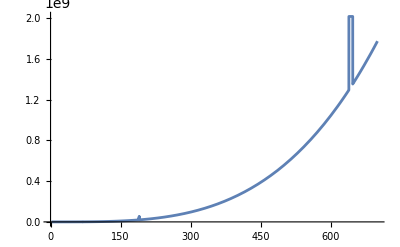

```mathematica
ListLinePlot[points]
```

```mathematica
Clear[n]
derivative=D[rc[x],x]
criticalPoints=Solve[derivative==0,x]
maximumValue=rc[x]/. x->x/. First[criticalPoints]
FullSimplify[maximumValue]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[(1-1/n^2)^x n^((8 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))/((1-(1-1/n^2)^x) n^0.51+4 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))) Log[1-1/n^2]+(1-1/n^2)^x n^((8 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))/((1-(1-1/n^2)^x) n^0.51+4 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))) Log[n] (-(8 (-(1-1/n^2)^x n^0.51 Log[1-1/n^2]-(4 (1-1/n^2)^x Log[1-1/n^2])/(Log[1-(1-1/n^2)^x]^2)) (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))/(((1-(1-1/n^2)^x) n^0.51+4 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))^2)-(8 (1-1/n^2)^x Log[1-1/n^2])/(Log[1-(1-1/n^2)^x]^2 ((1-(1-1/n^2)^x) n^0.51+4 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))))==0,x]

ReplaceAll::reps: {(1-Power[«2»])^x n^((8 (Times[«3»]+LogIntegral[«1»]))/Plus[«2»]) Log[1-Power[«2»]]+(1-Power[«2»])^x n^((8 (Times[«3»]+LogIntegral[«1»]))/Plus[«2»]) Log[n] (-(8 (Times[«4»]+Times[«4»]) (Times[«3»]+LogIntegral[«1»]))/Plus[«2»]^2-(8 Plus[«2»]^x Log[Plus[«2»]])/(Log[«1»]^2 Plus[«2»]))==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(1-1/n^2)^x n^((8 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))/((1-(1-1/n^2)^x) n^0.51+4 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x])))/.(1-1/n^2)^x n^((8 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))/((1-(1-1/n^2)^x) n^0.51+4 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))) Log[1-1/n^2]+(1-1/n^2)^x n^((8 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))/((1-(1-1/n^2)^x) n^0.51+4 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))) Log[n] (-(8 (-(1-1/n^2)^x n^0.51 Log[1-1/n^2]-(4 (1-1/n^2)^x Log[1-1/n^2])/(Log[1-(1-1/n^2)^x]^2)) (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))/(((1-(1-1/n^2)^x) n^0.51+4 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))^2)-(8 (1-1/n^2)^x Log[1-1/n^2])/(Log[1-(1-1/n^2)^x]^2 ((1-(1-1/n^2)^x) n^0.51+4 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))))==0

(1-1/n^2)^x n^(1/(1/2-((-1+(1-1/n^2)^x) n^0.51 Log[1-(1-1/n^2)^x])/(8 (-1+(1-1/n^2)^x+Log[1-(1-1/n^2)^x] LogIntegral[1-(1-1/n^2)^x]))))/.(1-1/n^2)^x n^(1/(1/2-((-1+(1-1/n^2)^x) n^0.51 Log[1-(1-1/n^2)^x])/(8 (-1+(1-1/n^2)^x+Log[1-(1-1/n^2)^x] LogIntegral[1-(1-1/n^2)^x])))) Log[1-1/n^2]+(8 (1-1/n^2)^(2 x) n^(((-1.+1. (1-1/n^2)^x) (-10.04+0.51 n^0.51 Log[1-(1-1/n^2)^x])-10.04 Log[1-(1-1/n^2)^x] LogIntegral[1-(1-1/n^2)^x])/((-1.+1. (1-1/n^2)^x) (-4.+1. n^0.51 Log[1-(1-1/n^2)^x])-4. Log[1-(1-1/n^2)^x] LogIntegral[1-(1-1/n^2)^x])) Log[1-1/n^2] Log[n] ((-1+(1-1/n^2)^x) (1+Log[1-(1-1/n^2)^x])+Log[1-(1-1/n^2)^x]^2 LogIntegral[1-(1-1/n^2)^x]))/(((-1+(1-1/n^2)^x) (-4+n^0.51 Log[1-(1-1/n^2)^x])-4 Log[1-(1-1/n^2)^x] LogIntegral[1-(1-1/n^2)^x])^2)==0

Bucle cortocircuito:

```mathematica
Clear[n]
Integrate[(1-b[x]/n^2)*n^(2*(g[b[x]/n^2])/(g[b[x]/n^2]+b[x]/2)), {n, 2, 5}]
```

∫_2^5 (1-1/n^2)^x n^(-(8 (1-(1-1/n^2)^x))/((1/2 (1-(1-1/n^2)^x) n^2-(4 (1-(1-1/n^2)^x))/Log[1-(1-1/n^2)^x]) Log[1-(1-1/n^2)^x]))ⅆn

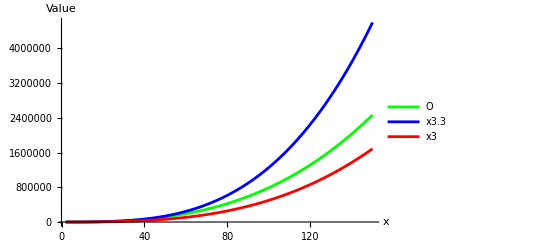

```mathematica
Clear[n]
integralFunction[q_?NumericQ]:=NIntegrate[(1-b[x]/n^2)*n^(2*(g[b[x]/n^2])/(g[b[x]/n^2] +b[x]/2)),{x,0, 2*q^3}, {n, 2, q}, Method->"GlobalAdaptive",MaxRecursion->15,WorkingPrecision->14]
Plot[{integralFunction[x], 0.5x^3.2, 0.5x^3},{x,2,150},PlotRange->All,AxesLabel->{"x","Value"}, PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.3","x3"}],Right]]
```

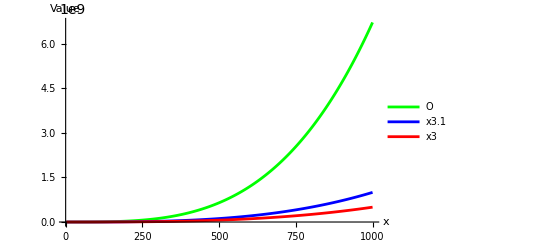

```mathematica
LaunchKernels[];
integralFunction[q_?NumericQ]:=NIntegrate[(1-b[x]/n^2)*n^(2*(g[b[x]/n^2])/(g[b[x]/n^2] +b[x]/Power[n,0.6])),{x,0, 3*q^3}, {n, 2, q}, Method->"GlobalAdaptive",MaxRecursion->15,WorkingPrecision->15]
points=ParallelTable[{x,Quiet[integralFunction[x]]},{x,2,1000}];
ListLinePlot[{points, Table[{x,0.5*x^3.1},{x,2,1000}], Table[{x,0.5*x^3},{x,2,1000}]},PlotRange->All,AxesLabel->{"x","Value"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.1","x3"}],Right]]
CloseKernels[];
```

Versión Integral de n (acumulando valores de n previos):

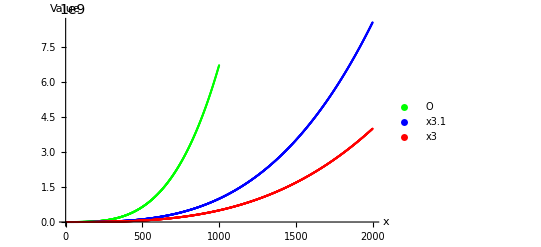

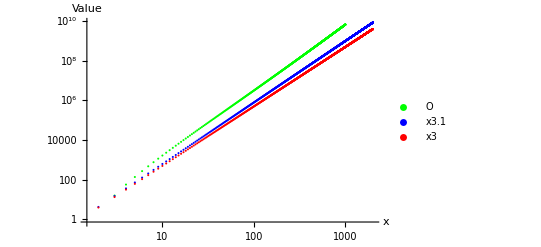

```mathematica
ListPlot[{points, Table[{x,0.5x^3.1},{x,2,2000}], Table[{x,0.5x^3},{x,2,2000}]},PlotRange->All,AxesLabel->{"x","Value"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.1","x3"}],Right]]
ListLogLogPlot[{points, Table[{x,0.5*x^3.1},{x,2,2000}], Table[{x,0.5x^3},{x,2,2000}]},PlotRange->All,AxesLabel->{"x","Value"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.1","x3"}],Right]]
```

{-0.286231508696904,3.3127956413227}

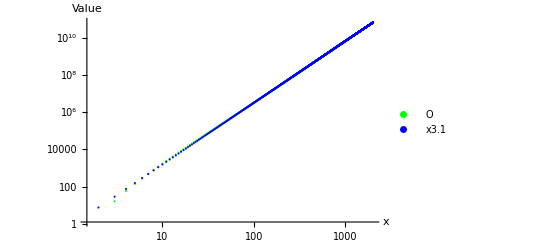

```mathematica
logYPoints={#[[1]],Log[#[[2]]]}&/@Rest[points];
linearModel=LinearModelFit[logYPoints,{Log[x]},x];
fittedLine=linearModel["Function"];
linearModel["BestFitParameters"]
ListLogLogPlot[{points, Table[{x,E^fittedLine[x]},{x,2,2000}]},PlotRange->All,AxesLabel->{"x","Value"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.1","x3"}],Right]]
```

FittedModel[0.491808046643693 x^3.37837298445595]

0.491808046643693 #1^3.37837298445595&

| DF | SS | MS
Model | 2 | 5.8322023811721×10^21 | 2.9161011905861×10^21
Error | 997 | 4.220651821×10^15 | 4.233351877×10^12
Uncorrected Total | 999 | 5.8322066018239×10^21 | 
Corrected Total | 998 | 3.466317803801×10^21 |

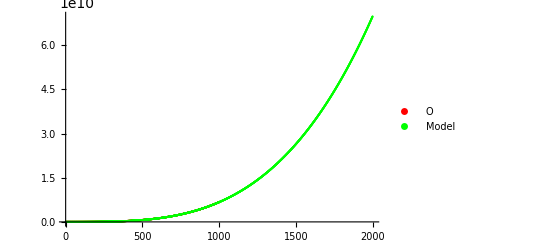

```mathematica
nonlinearModel=NonlinearModelFit[points,a*x^c ,{a,c},x]
nonlinearModel["Function"]
nonlinearModel["ANOVATable"]
ListPlot[{points, Table[{x, nonlinearModel[x]},{x,0,2000}]},PlotStyle->{Red, Green}, PlotLegends->Placed[LineLegend[Automatic,{"O","Model"}],Right]]
```

Pruebas con otras transformaciones:

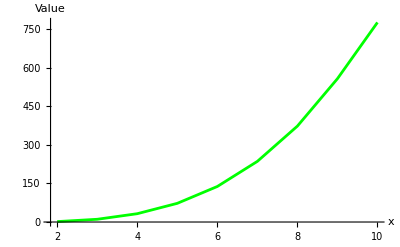

```mathematica
LaunchKernels[];
Clear[n]
points=ParallelTable[{n, Quiet[NIntegrate[(1-b[x]/n^2)*n^(2*(g[b[x]/n^2])/(g[b[x]/n^2] +b[x]/Power[n, 1.5])),{x,0,puntoEstab}]]},{n, 2, 40}];
ListLinePlot[{points},PlotRange->All,AxesLabel->{"x","Value"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.1","x3"}],Right]]
CloseKernels[];
```

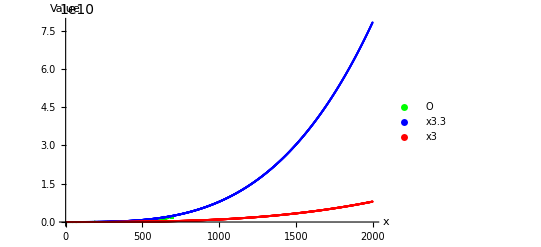

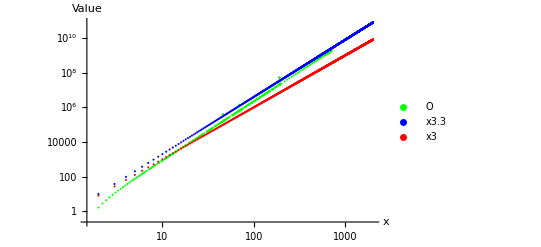

```mathematica
ListPlot[{points, Table[{x,x^3.3},{x,2,2000}], Table[{x,x^3},{x,2,2000}]},PlotRange->All,AxesLabel->{"x","Value"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.3","x3"}],Right]]
ListLogLogPlot[{points, Table[{x,x^3.3},{x,2,2000}], Table[{x,x^3},{x,2,2000}]},PlotRange->All,AxesLabel->{"x","Value"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.3","x3"}],Right]]
```

{-1.2067,3.43948}

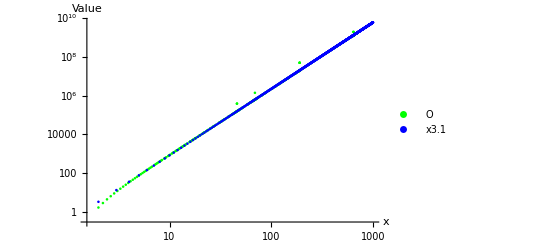

```mathematica
logYPoints={#[[1]],Log[#[[2]]]}&/@Rest[points];
linearModel=LinearModelFit[logYPoints,{Log[x]},x];
fittedLine=linearModel["Function"];
linearModel["BestFitParameters"]
ListLogLogPlot[{points, Table[{x,E^fittedLine[x]},{x,2,1000}]},PlotRange->All,AxesLabel->{"x","Value"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.1","x3"}],Right]]
```

FittedModel[0.414645 x^3.38627]

0.414645 #1^3.38627&

| DF | SS | MS
Model | 2 | 1.75938×10^20 | 8.79689×10^19
Error | 385 | 9.41839×10^17 | 2.44634×10^15
Uncorrected Total | 387 | 1.7688×10^20 | 
Corrected Total | 386 | 1.34895×10^20 |

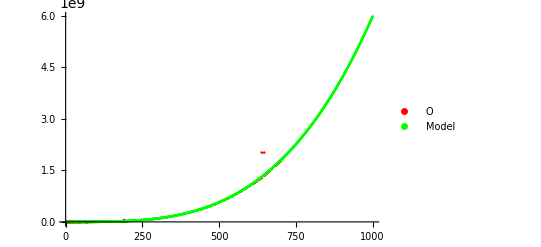

```mathematica
nonlinearModel=NonlinearModelFit[points,a*x^c ,{a,c},x]
nonlinearModel["Function"]
nonlinearModel["ANOVATable"]
ListPlot[{points, Table[{x, nonlinearModel[x]},{x,0,1000}]},PlotStyle->{Red, Green}, PlotLegends->Placed[LineLegend[Automatic,{"O","Model"}],Right]]
```